### Compute COM

#### Initialization Functions

```mathematica
boat[pow_] := 2*Abs[y/2]^pow≤z≤2
mass[n_]:=Integrate[1/4,{y,z}∈ImplicitRegion[boat[n],{y,z}]]
comY[n_?NumberQ]:=NIntegrate[y/4,{y,z}∈ImplicitRegion[boat[n],{y,z}],AccuracyGoal->5]/mass[n]
comZ[n_?NumberQ]:=NIntegrate[z/4,{y,z}∈ImplicitRegion[boat[n],{y,z}],AccuracyGoal->5]/mass[n]
```

```mathematica
RegionPlot[boat[2],{y,-2,2},{z,0,2},Axes->True,AxesLabel->Automatic,Frame->None]
```

```mathematica
Manipulate[Show[RegionPlot[boat[n],{y,-2,2},{z,0,2},Axes->True,AxesLabel->Automatic,Frame->None],Graphics[{PointSize[0.025],Point[{comY[n],comZ[n]}]}]],{n,{1,2,3,4,10}}]
```

ImplicitRegion::bcond: boat[1] should be a Boolean combination of equations, inequalities, and Element statements.

ImplicitRegion::bcond: ImplicitRegion[ⅇ^(2.5 Abs[Power[«2»] y])+1/6 (-4+x^2)≤z≤1,{x,y,z}][1] should be a Boolean combination of equations, inequalities, and Element statements.

### Find Waterline (at angle):

```mathematica
water[theta_, b_] := If[theta==π/2,0≤y≤2&&0≤z≤2,If[theta<π/2,z≤Tan[theta]*y+b,z≥Tan[theta]*y+b]]
submergedRegion[n_,theta_,b_] := boat[n] && water[theta,b]
massOfWater[n_,theta_,b_]:=Integrate[1,{y,z}∈ImplicitRegion[submergedRegion[n,theta,b],{y,z}]]
findB[n_,theta_] :=FindRoot[mass[n]-massOfWater[n,theta,b]==0,{b,1}]
```

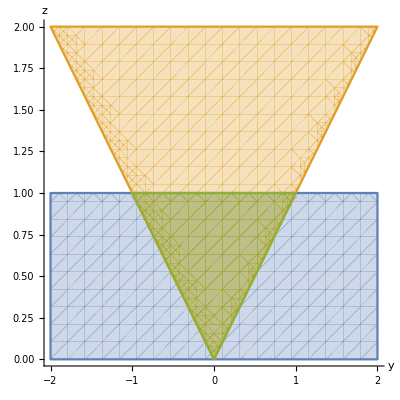

```mathematica
RegionPlot[{water[0,b/.findB[1,0][[1]]],boat[1],submergedRegion[1,0,b/.findB[1,0]]},{y,-2,2},{z,0,2},Axes->True,AxesLabel->Automatic,Frame->None]
```

```mathematica
findB[1,0]
```

{b→1.}

```mathematica
Clear[b]
ang=3π/4;
boatNum = 2;
mass[boatNum]/massOfWater[boatNum,ang,b/.findB[boatNum,ang]]
```

1.

0

0.793701

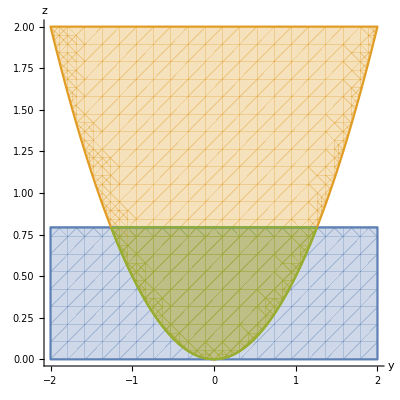

```mathematica
angle = 0
yIntercept = b/.findB[2,angle][[1]]
RegionPlot[{water[angle,yIntercept],boat[2],submergedRegion[2,angle,yIntercept]},{y,-2,2},{z,0,2},Axes->True,AxesLabel->Automatic,Frame->None]
```

### Find COB:

```mathematica
cobY[n_,theta_]:=Integrate[y,{y,z}∈ImplicitRegion[submergedRegion[n,theta,b/.findB[n,theta]],{y,z}]]/massOfWater[n,theta,b/.findB[n,theta]]
cobZ[n_,theta_]:=Integrate[z,{y,z}∈ImplicitRegion[submergedRegion[n,theta,b/.findB[n,theta]],{y,z}]]/massOfWater[n,theta,b/.findB[n,theta]]
```

```mathematica
Clear[b]
Manipulate[Show[RegionPlot[{water[angle, b/.findB[boatNum,angle]],boat[boatNum],submergedRegion[boatNum,angle, b/.findB[boatNum,angle]]},{y,-2,2},{z,0,2},Axes->True,AxesLabel->Automatic,Frame->None],
Graphics[{PointSize[0.025],Point[{cobY[boatNum,angle],cobZ[boatNum,angle]}]}],
Graphics[{PointSize[0.025],Point[{comY[boatNum],comZ[boatNum]}]}]],{boatNum,{1,2,3,4,20}},{angle,{0,π/12,π/6,π/4,π/3,π/2,2π/3,3π/4}}]
```

NIntegrate::femtemnbb: The bounds for ImplicitRegion[ⅇ^(1. Abs[Times[«2»]])+1/6 (-4+x^2)≤z≤1&&z≤0.5-0.267949 y&&x≥0,{x,y,z}] are {{-∞,∞},{-∞,∞},{-∞,∞}}. Unless finite numeric bounds are specified, the mesh generation will constrain the region to have finite bounds.

ReplaceAll::reps: {findB[1.,0.261799]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ImplicitRegion::bcond: water[π/12,b/.findB[1,π/12]] should be a Boolean combination of equations, inequalities, and Element statements.

ImplicitRegion::bcond: boat[1] should be a Boolean combination of equations, inequalities, and Element statements.

ImplicitRegion::bcond: submergedRegion[1,π/12,b/.findB[1,π/12]] should be a Boolean combination of equations, inequalities, and Element statements.

General::stop: Further output of ImplicitRegion::bcond will be suppressed during this calculation.

ReplaceAll::reps: {findB[1.,0.261799]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ImplicitRegion::bcond: water[π/12,b/.findB[1,π/12]] should be a Boolean combination of equations, inequalities, and Element statements.

ImplicitRegion::bcond: boat[1] should be a Boolean combination of equations, inequalities, and Element statements.

ImplicitRegion::bcond: submergedRegion[1,π/12,b/.findB[1,π/12]] should be a Boolean combination of equations, inequalities, and Element statements.

General::stop: Further output of ImplicitRegion::bcond will be suppressed during this calculation.

ReplaceAll::reps: {findB[1.,0.261799]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ImplicitRegion::bcond: boat[1] should be a Boolean combination of equations, inequalities, and Element statements.

ImplicitRegion::bcond: submergedRegion[1,π/12,b/.findB[1,π/12]] should be a Boolean combination of equations, inequalities, and Element statements.

ReplaceAll::reps: {findB[1.,0.261799]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ImplicitRegion::bcond: water[π/12,b/.findB[1,π/12]] should be a Boolean combination of equations, inequalities, and Element statements.

ImplicitRegion::bcond: ImplicitRegion[ⅇ^(2.5 Abs[Power[«2»] y])+1/6 (-4+x^2)≤z≤1,{x,y,z}][1] should be a Boolean combination of equations, inequalities, and Element statements.

ImplicitRegion::bcond: submergedRegion[1,π/12,b/.findB[1,π/12]] should be a Boolean combination of equations, inequalities, and Element statements.

General::stop: Further output of ImplicitRegion::bcond will be suppressed during this calculation.

### Computing Moment

```mathematica
buoyForce[n_,theta_]:=mass[n]*(9.81)
momentArm[n_,theta_]:={cobY[n,theta]-comY[n],cobZ[n,theta]-comZ[n],0}
moment[n_,theta_]:=momentArm[n,theta]×{buoyForce[n,theta]*-Sin[theta],buoyForce[n,theta]*Cos[theta],0}
```

```mathematica
momentArm[1,π/3]
moment[1,π/3]
```

{0.973276,-0.0496545,0}

{0.,0.,5.19577}

```mathematica
angles = Range[0,π,.1]

momentPoints = moment[1,#]&/@angles
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1}

{{0.,0.,0.},{0.,0.,0.00662293},{0.,0.,0.0550937},{0.,0.,0.199366},{0.,0.,0.527071},{0.,0.,1.21595},{0.,0.,2.39174},{0.,0.,3.2382},{0.,0.,3.78197},{0.,0.,4.11661},{0.,0.,4.30282},{0.,0.,4.38438},{0.,0.,4.23839},{0.,0.,3.80042},{0.,0.,3.19088},{0.,0.,2.47109},{0.,0.,1.67798},{0.,0.,0.837239},{0.,0.,-0.0310589},{0.,0.,-0.909815},{0.,0.,-1.78345},{0.,0.,-2.637},{0.,0.,-3.45537},{0.,0.,-4.22254},{0.,0.,-4.92025},{0.,0.,-5.52583},{0.,0.,-6.00757},{0.,0.,-6.31447},{0.,0.,-6.34933},{0.,0.,-5.88224},{0.,0.,-4.15272},{0.,0.,-1.19688}}

```mathematica
moments = momentPoints[[All,3]]
points = Transpose[{angles,moments}]
```

{0.,0.00662293,0.0550937,0.199366,0.527071,1.21595,2.39174,3.2382,3.78197,4.11661,4.30282,4.38438,4.23839,3.80042,3.19088,2.47109,1.67798,0.837239,-0.0310589,-0.909815,-1.78345,-2.637,-3.45537,-4.22254,-4.92025,-5.52583,-6.00757,-6.31447,-6.34933,-5.88224,-4.15272,-1.19688}

{{0.,0.},{0.1,0.00662293},{0.2,0.0550937},{0.3,0.199366},{0.4,0.527071},{0.5,1.21595},{0.6,2.39174},{0.7,3.2382},{0.8,3.78197},{0.9,4.11661},{1.,4.30282},{1.1,4.38438},{1.2,4.23839},{1.3,3.80042},{1.4,3.19088},{1.5,2.47109},{1.6,1.67798},{1.7,0.837239},{1.8,-0.0310589},{1.9,-0.909815},{2.,-1.78345},{2.1,-2.637},{2.2,-3.45537},{2.3,-4.22254},{2.4,-4.92025},{2.5,-5.52583},{2.6,-6.00757},{2.7,-6.31447},{2.8,-6.34933},{2.9,-5.88224},{3.,-4.15272},{3.1,-1.19688}}

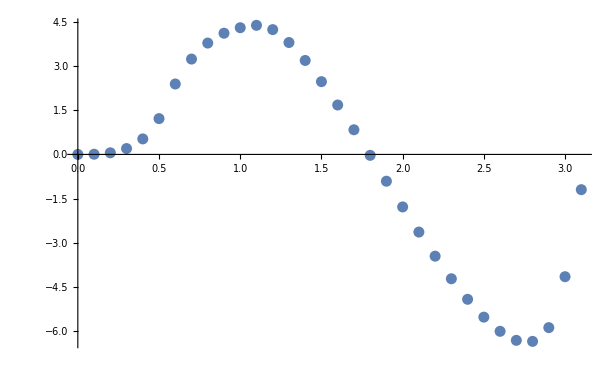

```mathematica
ListPlot[points,Axes->True,AxesLabel->Automatic,Frame->None]
```

### 3D Boat Calculations

```mathematica
boat3D[beam_,draft_,length_]:=draft*((2x/length)^4+(2y/beam)^2)≤z≤draft
boatCross[beam_,draft_,length_,xVal_]:=draft*((2*xVal/length)^4+(2y/beam)^2)≤z≤draft
boatProfile[draft_,length_] :=draft*((2*x/length)^4)≤z≤draft
boatDeck[beam_,length_]:=((2*x/length)^4+(2*y/beam)^2)≤1
```

```mathematica
Manipulate[RegionPlot3D[boat3D[b,d,l],{x,-2,2},{y,-2,2},{z,0,4},Axes->True,AxesLabel->Automatic],{b,1,4},{d,1,4},{l,1,4}]
```

RegionPlot3D::boolf: boat3D[1.235,2.92,3.84] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: boat3D[1.235,2.92,3.84] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: boat3D[1.235,2.92,3.84] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: boat3D[1.235,2.92,3.84] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: boat3D[1.235,2.92,3.84] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: boat3D[1.235,2.92,3.84] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: boat3D[1.235,2.92,3.84] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

```mathematica
Manipulate[RegionPlot[boatCross[b,d,l,0],{y,-2,2},{z,0,4},Axes->True,AxesLabel->Automatic],{b,1,4},{d,1,4},{l,1,4},{xPoint,-1,1}]
```

ImplicitRegion::bcond: boatCross[2.885,1.965,3.81,0] should be a Boolean combination of equations, inequalities, and Element statements.

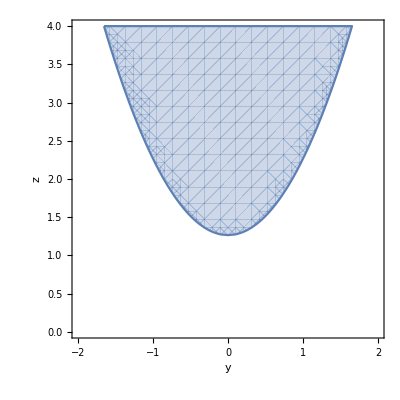

```mathematica
RegionPlot[boatCross[4,4,4,1.5],{y,-2,2},{z,0,4},Axes->True,AxesLabel->Automatic]
```

```mathematica
Manipulate[RegionPlot[boatProfile[b,d],{x,-2,2},{z,0,4},Axes->True,AxesLabel->Automatic],{b,1,4},{d,1,4}]
```

ImplicitRegion::bcond: boatProfile[1.87,3.27] should be a Boolean combination of equations, inequalities, and Element statements.

```mathematica
Manipulate[RegionPlot[boatDeck[b,l],{x,-2,2},{y,-2,2},Axes->True,AxesLabel->Automatic],{b,1,4},{l,1,4}]
```

ImplicitRegion::bcond: boatDeck[1.38,3.79] should be a Boolean combination of equations, inequalities, and Element statements.

```mathematica
comZ[.5]
```

3.45686